```mathematica
(********************* CONDITIONS FOR HAVING 1, 2 or 3 INFLECTIONS - dervied in EqS98toS100.nb *********************)
```

```mathematica
(*Whith this new information, let's simplify the conditions*)
b1[a_]:=Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,1]
b2[a_]:=Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,2]
b3[a_]:=Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,3]
Inflection1[a_,b_]:=(a<=b<=b1[a])||(b3[a]≥b≥b2[a]&& 2<=a<=Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753)||a==0;
Inflection2[a_,b_]:=(a>0&&0<b<a)||(a<0&&b>0);
Inflection3[a_,b_]:=b>b1[a] && ((b>b3[a]||b2[a]>b )&&2<= a<=Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753);
```

```mathematica
(********************* EQUIVALENT FORMULATION FOR 3 INFLECTIONS - EqS101 *********************)
```

```mathematica
bcutoff[a_]:=If[2<= a<=Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753&&Im[b2[a]]==0&&Im[b3[a]]==0,Max[b1[a],b2[a],b3[a]],b1[a]]
Inflection3cutoff[a_,b_]:=b>bcutoff[a];
```

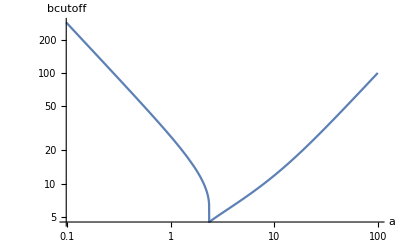

```mathematica
LogLogPlot[bcutoff[a],{a,0,100},AxesLabel->{"a","bcutoff"}]
```

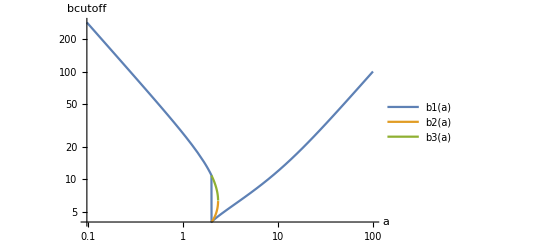

```mathematica
LogLogPlot[{b1[a],b2[a],b3[a]},{a,0,100},AxesLabel->{"a","bcutoff"},PlotLegends->{"b1(a)","b2(a)","b3(a)"}]
```